```mathematica
SetDirectory[NotebookDirectory[]]
Import["GraphPartition.m"]
<< GraphPartition`
<< Combinatorica`
$Context
```

C:\Users\Chuqian\Desktop\research\graphPartitioning

General::compat: Combinatorica Graph and Permutations functionality has been superseded by preloaded functionality. The package now being loaded may conflict with this. Please see the Compatibility Guide for details.

Global`

```mathematica
ga=RoachGraph[10]
ga = SetVertexWeights[ga, Table[1/V[ga],V[ga]]]
VertexWeights[ga]
(*ShowGraph[ga]*)
```

⁃Graph:<23,20,Undirected>⁃

⁃Graph:<23,20,Undirected>⁃

{1/20,1/20,1/20,1/20,1/20,1/20,1/20,1/20,1/20,1/20,1/20,1/20,1/20,1/20,1/20,1/20,1/20,1/20,1/20,1/20}

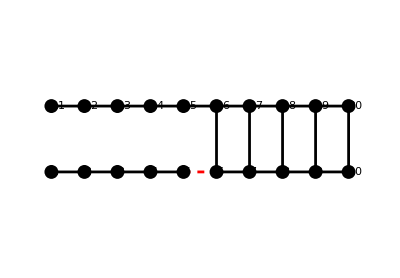

{0.409186,0.380021,0.323768,0.244438,0.147685,0.040405,0.0110555,0.00302894,0.000844355,0.000288302,-0.409186,-0.380021,-0.323768,-0.244438,-0.147685,-0.040405,-0.0110555,-0.00302894,-0.000844355,-0.000288302}

-Graphics-

-Graphics-

```mathematica
GraphPartition`ShowSpectralCut[ga]
FiedlerVector[ga]
(* what are the actual score in the sweep cut
*)GraphPartition`ShowIsoperimetricCut[SetVertexWeights[ga]]
GraphPartition`ShowMultipleFiedlerCut[ga]
(*
ShowGraph[GraphPartition`MultipleFiedlerCut[ga]]

*)
```

```mathematica
{0.40918635159651134,0.380020550398621,0.3237678148961186,0.2444377023337704,0.14768466888532764,0.040405033863103464,0.01105549469010167,0.003028936306558162,0.0008443553729352688,0.0002883016017182509,-0.40918635159650696,-0.38002055039861754,-0.3237678148961161,-0.24443770233376955,-0.14768466888532883,-0.040405033863106836,-0.01105549469010684,-0.003028936306564904,-0.0008443553729435061,-0.00028830160172692776}
```

```mathematica
ga=SetVertexWeights[ga,Table[1,1/V[ga]]]
EvaluatePartitionAlg[alg_,g_] := Switch[alg,
SpectralAlg,
Flatten[Timing[SpectralEdges[g, IncludeObj->True]],1],
IsoperimetricAlg,
Flatten[Timing[IsoperimetricEdges[g, IncludeObj->True]],1],
MultipleFiedlerAlg,
Flatten[Timing[MultipleFiedlerEdges[g, IncludeObj->True]],1](*
EvaluateMultipleFiedlerEdges[ga]*)
]
```

⁃Graph:<23,20,Undirected>⁃

⁃Graph:<23,20,Undirected>⁃

{1/20,1/20,1/20,1/20,1/20,1/20,1/20,1/20,1/20,1/20,1/20,1/20,1/20,1/20,1/20,1/20,1/20,1/20,1/20,1/20}

{0.015625,16/3,{{5,6}}}

-Graphics-

{0.03125,8,{{5,6},{15,16}}}

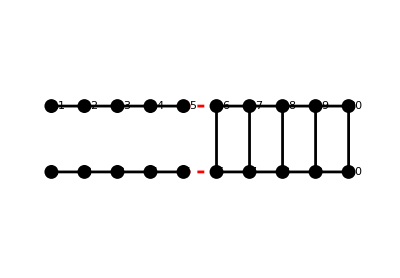

{0.125,16/3,{{5,6}}}

-Graphics-

{1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

{1/4,3/4}

```mathematica
ga=SetVertexWeights[ga,Table[1/V[ga],V[ga]]]
VertexWeights[ga]
{t, objFn, cutEdges}=EvaluatePartitionAlg[SpectralAlg,ga ]
ShowCuttedEdges[ga, cutEdges]
(*ShowCuttedEdges[ga,cutEdges]
v=FiedlerVector[ga]
c=CriterionCut[ga,v]
partitionWeights=PartitionWeights[VertexWeights[ga],v,c]
Total[Map[LookupWeight[ga,#]&,VectorCut[ga,v,c]]]
*){t, objFn, cutEdges}=EvaluatePartitionAlg[IsoperimetricAlg,ga ]
ShowCuttedEdges[ga, cutEdges]
{t, objFn, cutEdges}=EvaluatePartitionAlg[MultipleFiedlerAlg,ga ]

ShowCuttedEdges[ga, cutEdges]
v=MultipleFiedlerVector[ga]
partitionWeights=PartitionWeights[VertexWeights[ga],v,0.5]
```

```mathematica
Plot performances on RoachGraphs
```

```mathematica
graphs = Map[SetVertexWeights[RoachGraph[#],Table[1/(#*2),#*2]]&, Range[10,100,20]]
SpectralMetrics = Map[EvaluatePartitionAlg[SpectralAlg, #]&, graphs];
SpectralTimes = Transpose[SpectralMetrics][[1]]
SpectralObjs = Transpose[SpectralMetrics][[2]]
IsoperimetricMetrics = Map[EvaluatePartitionAlg[IsoperimetricAlg, #]&, graphs];
IsoperimetricTimes = Transpose[IsoperimetricMetrics][[1]]
IsoperimetricObjs = Transpose[IsoperimetricMetrics][[2]]
MultipleFiedlerMetrics = Map[EvaluatePartitionAlg[MultipleFiedlerAlg, #]&, graphs];
MultipleFiedlerTimes = Transpose[MultipleFiedlerMetrics][[1]]
MultipleFiedlerObjs = Transpose[MultipleFiedlerMetrics][[2]]
```

{⁃Graph:<23,20,Undirected>⁃,⁃Graph:<73,60,Undirected>⁃,⁃Graph:<123,100,Undirected>⁃,⁃Graph:<173,140,Undirected>⁃,⁃Graph:<223,180,Undirected>⁃}

{0.015625,0.09375,0.375,0.796875,1.26563}

{16/3,16/3,16/3,16/3,16/3}

{0.015625,0.09375,0.25,0.515625,0.734375}

{8,225/28,8,9800/1189,8}

{0.078125,1.78125,9.71875,29.8125,67.375}

{16/3,16/3,16/3,16/3,16/3}

{Spectral,Isoperimetric,MultipleFiedler}

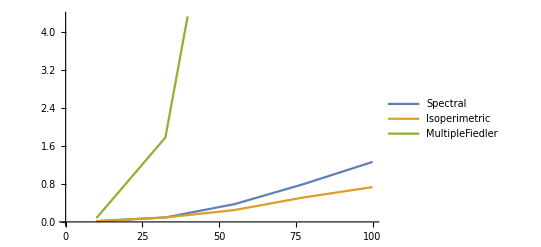

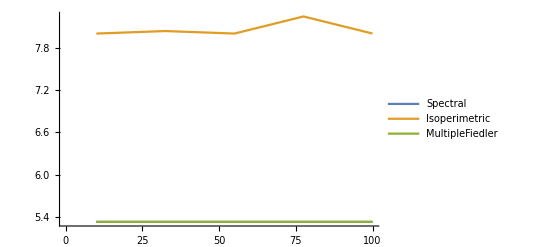

```mathematica
legends = {"Spectral","Isoperimetric","MultipleFiedler"}
ListLinePlot[{SpectralTimes, IsoperimetricTimes, MultipleFiedlerTimes},PlotLegends->legends, DataRange->{10,100}]
ListLinePlot[{SpectralObjs, IsoperimetricObjs, MultipleFiedlerObjs}, PlotLegends->legends, DataRange->{10,100}]
```

```mathematica
graphs = Map[SetVertexWeights[RandomTree[#],Table[1/#,#]]&, Range[10,100,20]]
SpectralMetrics = Map[EvaluatePartitionAlg[SpectralAlg, #]&, graphs];
SpectralTimes = Transpose[SpectralMetrics][[1]]
SpectralObjs = Transpose[SpectralMetrics][[2]]
IsoperimetricMetrics = Map[EvaluatePartitionAlg[IsoperimetricAlg, #]&, graphs];
IsoperimetricTimes = Transpose[IsoperimetricMetrics][[1]]
IsoperimetricObjs = Transpose[IsoperimetricMetrics][[2]]
MultipleFiedlerMetrics = Map[EvaluatePartitionAlg[MultipleFiedlerAlg, #]&, graphs];
MultipleFiedlerTimes = Transpose[MultipleFiedlerMetrics][[1]]
MultipleFiedlerObjs = Transpose[MultipleFiedlerMetrics][[2]]
```

{⁃Graph:<9,10,Undirected>⁃,⁃Graph:<29,30,Undirected>⁃,⁃Graph:<49,50,Undirected>⁃,⁃Graph:<69,70,Undirected>⁃,⁃Graph:<89,90,Undirected>⁃}

{0.,0.015625,0.046875,0.078125,0.140625}

{25/6,225/56,4,4900/1209,225/56}

{0.015625,0.046875,0.078125,0.109375,0.203125}

{25/6,900/161,2500/609,1225/264,81/20}

{0.015625,0.25,1.03125,2.98438,6.85938}

{25/6,100/7,16,1225/216,162/7}

{Spectral,Isoperimetric,MultipleFiedler}

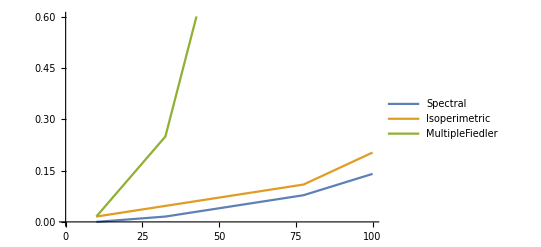

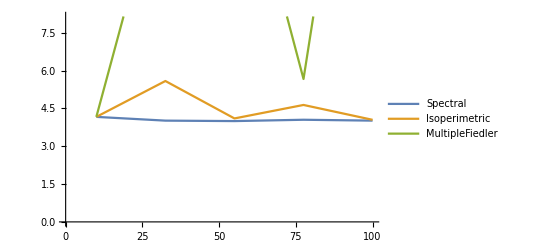

```mathematica
legends = {"Spectral","Isoperimetric","MultipleFiedler"}
ListLinePlot[{SpectralTimes, IsoperimetricTimes, MultipleFiedlerTimes},PlotLegends->legends, DataRange->{10,100}]
ListLinePlot[{SpectralObjs, IsoperimetricObjs, MultipleFiedlerObjs}, PlotLegends->legends, DataRange->{10,100}]
```

```mathematica
SpectralMetrics = Table[EvaluatePartitionAlg[SpectralAlg, graph],{graph,graphs}]
```

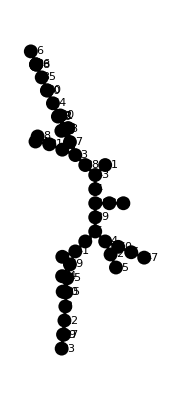

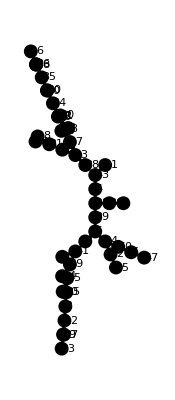

```mathematica
ShowSpectralCut[graphs[[3]]]
ShowMultipleFiedlerCut[graphs[[3]]]
```

# Small experiments 1. Develop evaluation matrix - Runtime - ObjectiveFunction - Parameters Spectral Partitioning - Isoperimetric Partitioning -> The Ground Vertex -> The number of iterations Multiple Fiedler Vector -> The # of eigenvectors -> Spectral Vertex Choice heuristic 2. Find dataset & benchmarks -> RandomTree, RoachGraphs -> DIMACS Graph Partitioning and Graph Clustering http://www.cc.gatech.edu/dimacs10/downloads.shtml -> Chris Walshaw’s graph partitioning archive http://chriswalshaw.co.uk/partition/ http://www.cc.gatech.edu/dimacs10/archive/data/walshaw/ -> Graph partitioning training examples http://eniac.cyi.ac.cy/display/UserDoc/Graph+Partitioning+Training+Examples#GraphPartitioningTrainingExamples-Example1

Why multiple Fiedler is performing worse.
VectorParition : how to decide eta
Metrics : time, CriterionFunction
Other data to test on

1) Generate normal graph data

- walk through every vertex and connect with 3 other random vertex
*- points on grid and connect with points within distance
(with locality)
- triangulation hhfhk

2) Debug spectral &  multiple fielder

currency in Canada US not let to use card or (insisting on 1 currency )

## Debugging Spectral Partitioning result: Criterion Cut needs to check a broader range of possible cuts

```mathematica
ga=RoachGraph[10];
ga = SetVertexWeights[ga, Table[1/V[ga],V[ga]]];
GraphPartition`ShowSpectralCut[ga]
v = FiedlerVector[ga]
Table[{i,v[[i]]},{i,1,Length[v]}]
EvaluatePartitionAlg[SpectralAlg, ga]
```

```mathematica
c=v[[16]]
N[CriterionPartitionFunction[ga,v, c]]
VectorCut[ga,v,c]
PartitionWeights[VertexWeights[ga],v,c]
N[CriterionCut[ga,v,IncludeCut->True, Range->{1/10,1}]]
```

```mathematica
Debugging Multiple Fiedler
```

Need to try different values of mu
Need to truncate to k eigenvectors
Need to implement the Mass matrix

```mathematica
ga = GridGraph[5,2];
ga = SetVertexWeights[ga, Table[1/V[ga],V[ga]]];
ShowSpectralCut[ga]
(*ShowIsoperimetricCut[ga]*)
(*ShowMultipleFiedlerCut[ga]*)
MatrixForm[SpectralVectors[ga]]
```

```mathematica
MultipleFiedlerVector[ga]
```

```mathematica
eigenvalues=Reverse[First[Eigensystem[N[LaplacianMatrix[ga]]]]]
eigenvectors=Reverse[Last[Eigensystem[N[LaplacianMatrix[ga]]]]];

MatrixForm[eigenvectors]
```

```mathematica
labelledVectors=MapIndexed[ {#1, #2[[1]]}&,SpectralVectors[ga]]
```

```mathematica
VV=Table[Normalize[v],{v,es[[2]]}];
Dimensions[VV]
 LL=DiagonalMatrix[es[[1]]];
Transpose[VV].LL.VV
GraphPartition`LaplacianMatrix[ga]
```

```mathematica
Maximum[v,-CriterionPartitionFunction[g,#,0.5]&]
```

```mathematica
Clear[MultipleFiedlerVector]
```

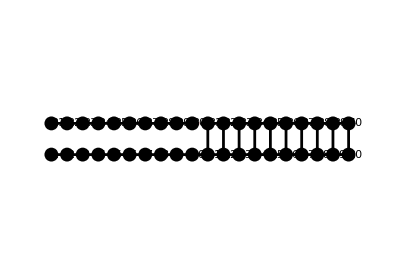

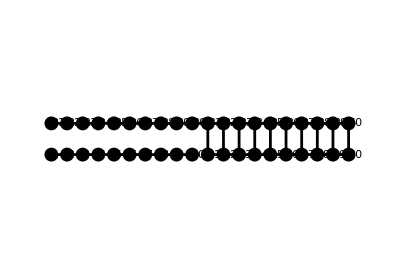

```mathematica
ga=RoachGraph[20];
ga = SetVertexWeights[ga, Table[1/V[ga],V[ga]]];
ShowSpectralCut[ga]
ShowMultipleFiedlerCut[ga]
```

```mathematica
MatrixForm[s= SpectralVectors[ga]]
```

(-0.538111 | 0.97863 | -0.745255 | 0.699483 | 0.864428 | -0.627944 | 0.537208 | -0.660516 | 0.435389 | 0.124767 | 0.379902 | 0.331108 | -0.232355 | 0.232188 | 0.197078 | 0.144057 | -0.0679933 | -0.0409061 | 0.00203153 | 0.00011014
-0.538111 | 0.908876 | -0.672304 | 0.432304 | 0.336156 | -0.110248 | -0.205195 | 0.351196 | -0.435389 | -0.136443 | -0.584414 | -0.535744 | 0.446724 | -0.505142 | -0.508613 | -0.377147 | 0.197324 | 0.12152 | -0.00804472 | -0.000519859
-0.538111 | 0.774339 | -0.533544 | -7.98851×10^-16 | -0.397548 | 0.498339 | -0.664026 | 0.824982 | -0.435389 | -0.111998 | -0.0652957 | -1.61924×10^-15 | -0.179792 | 0.361642 | 0.606918 | 0.466179 | -0.30734 | -0.198576 | 0.0217802 | 0.00182373
-0.538111 | 0.584609 | -0.342556 | -0.432304 | -0.888302 | 0.696081 | -0.205195 | 0.0351447 | 0.435389 | 0.146924 | 0.619564 | 0.535744 | -0.280848 | 0.0800066 | -0.450781 | -0.377147 | 0.387271 | 0.269816 | -0.0564232 | -0.00626439
-0.538111 | 0.35321 | -0.118037 | -0.699483 | -0.836194 | 0.319953 | 0.537208 | -0.808524 | 0.435389 | 0.0982482 | -0.268233 | -0.331108 | 0.438902 | -0.455695 | 0.105661 | 0.144057 | -0.429293 | -0.333154 | 0.145228 | 0.0214797
-0.538111 | 0.0966347 | 0.118037 | -0.699483 | -0.273068 | -0.319953 | 0.537208 | -0.413777 | -0.435389 | -0.156118 | -0.475167 | -0.331108 | -0.124082 | 0.455695 | 0.283757 | 0.144057 | 0.429293 | 0.386736 | -0.373441 | -0.07364
-0.538111 | 0.0264409 | 0.342556 | -0.432304 | -0.0892017 | -0.696081 | -0.205195 | -0.212804 | -0.435389 | -0.395875 | -0.426305 | 0.535744 | -0.572589 | -0.0800066 | 0.0133003 | -0.377147 | -0.387271 | 0.34448 | 0.213248 | 0.10518
-0.538111 | 0.00724415 | 0.533544 | -7.1009×10^-16 | -0.0292253 | -0.498339 | -0.664026 | -0.111487 | 0.435389 | -0.598584 | -0.147951 | -1.48328×10^-16 | -0.492826 | -0.361642 | -0.278181 | 0.466179 | 0.30734 | -0.376647 | 0.168739 | -0.107269
-0.538111 | 0.0020194 | 0.672304 | 0.432304 | -0.00983928 | 0.110248 | -0.205195 | -0.0623793 | 0.435389 | -0.745275 | 0.210049 | -0.535744 | 0.0416164 | 0.505142 | -0.129924 | -0.377147 | -0.197324 | -0.35551 | -0.375225 | 0.0793209
-0.538111 | 0.000689516 | 0.745255 | 0.699483 | -0.00411879 | 0.627944 | 0.537208 | -0.042484 | -0.435389 | -0.822221 | 0.454974 | 0.331108 | 0.537664 | -0.232188 | 0.223712 | 0.144057 | 0.0679933 | 0.366236 | 0.191449 | -0.0291622
-0.538111 | -0.97863 | -0.745255 | 0.699483 | -0.864428 | -0.627944 | 0.537208 | 0.660516 | 0.435389 | -0.124767 | -0.379902 | 0.331108 | 0.232355 | 0.232188 | -0.197078 | 0.144057 | -0.0679933 | 0.0409061 | -0.00203153 | -0.00011014
-0.538111 | -0.908876 | -0.672304 | 0.432304 | -0.336156 | -0.110248 | -0.205195 | -0.351196 | -0.435389 | 0.136443 | 0.584414 | -0.535744 | -0.446724 | -0.505142 | 0.508613 | -0.377147 | 0.197324 | -0.12152 | 0.00804472 | 0.000519859
-0.538111 | -0.774339 | -0.533544 | -6.45536×10^-16 | 0.397548 | 0.498339 | -0.664026 | -0.824982 | -0.435389 | 0.111998 | 0.0652957 | 1.26079×10^-15 | 0.179792 | 0.361642 | -0.606918 | 0.466179 | -0.30734 | 0.198576 | -0.0217802 | -0.00182373
-0.538111 | -0.584609 | -0.342556 | -0.432304 | 0.888302 | 0.696081 | -0.205195 | -0.0351447 | 0.435389 | -0.146924 | -0.619564 | 0.535744 | 0.280848 | 0.0800066 | 0.450781 | -0.377147 | 0.387271 | -0.269816 | 0.0564232 | 0.00626439
-0.538111 | -0.35321 | -0.118037 | -0.699483 | 0.836194 | 0.319953 | 0.537208 | 0.808524 | 0.435389 | -0.0982482 | 0.268233 | -0.331108 | -0.438902 | -0.455695 | -0.105661 | 0.144057 | -0.429293 | 0.333154 | -0.145228 | -0.0214797
-0.538111 | -0.0966347 | 0.118037 | -0.699483 | 0.273068 | -0.319953 | 0.537208 | 0.413777 | -0.435389 | 0.156118 | 0.475167 | -0.331108 | 0.124082 | 0.455695 | -0.283757 | 0.144057 | 0.429293 | -0.386736 | 0.373441 | 0.07364
-0.538111 | -0.0264409 | 0.342556 | -0.432304 | 0.0892017 | -0.696081 | -0.205195 | 0.212804 | -0.435389 | 0.395875 | 0.426305 | 0.535744 | 0.572589 | -0.0800066 | -0.0133003 | -0.377147 | -0.387271 | -0.34448 | -0.213248 | -0.10518
-0.538111 | -0.00724415 | 0.533544 | -1.74295×10^-15 | 0.0292253 | -0.498339 | -0.664026 | 0.111487 | 0.435389 | 0.598584 | 0.147951 | 6.92196×10^-16 | 0.492826 | -0.361642 | 0.278181 | 0.466179 | 0.30734 | 0.376647 | -0.168739 | 0.107269
-0.538111 | -0.0020194 | 0.672304 | 0.432304 | 0.00983928 | 0.110248 | -0.205195 | 0.0623793 | 0.435389 | 0.745275 | -0.210049 | -0.535744 | -0.0416164 | 0.505142 | 0.129924 | -0.377147 | -0.197324 | 0.35551 | 0.375225 | -0.0793209
-0.538111 | -0.000689516 | 0.745255 | 0.699483 | 0.00411879 | 0.627944 | 0.537208 | 0.042484 | -0.435389 | 0.822221 | -0.454974 | 0.331108 | -0.537664 | -0.232188 | -0.223712 | 0.144057 | 0.0679933 | -0.366236 | -0.191449 | 0.0291622)

```mathematica
Norm[Sum[s[[i]],{i,1,5}]+Sum[s[[i]],{i,11,15}]]
```

7.47748

```mathematica
Norm[Sum[s[[i]],{i,1,10}]]
```

7.27411